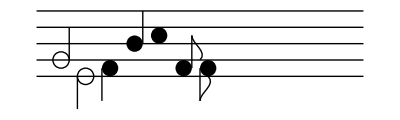

```mathematica
drawStaff[cent_,len_]:={Line[{{0,cent+4},{len,cent+4}}],Line[{{0,cent+2},{len,cent+2}}],Line[{{0,cent},{len,cent}}],Line[{{0,cent-2},{len,cent-2}}],Line[{{0,cent-4},{len,cent-4}}]};

drawWholeNote[step_] :=
(horzPos +=spacing;
{Disk[{horzPos, step}, 1]})
drawHalfNoteDown[step_] :=
(horzPos +=spacing;
{Circle[{horzPos, step}], Line[{{horzPos-1,step},{horzPos-1,step-4}}]})
drawHalfNoteUp[step_] :=
(horzPos +=spacing;
{Circle[{horzPos, step}], Line[{{horzPos+1,step},{horzPos+1,step+4}}]})
drawQuarterNoteDown[step_] :=
(horzPos +=spacing;
{Disk[{horzPos, step}], Line[{{horzPos-1,step},{horzPos-1,step-4}}]})
drawQuarterNoteUp[step_] :=
(horzPos +=spacing;
{Disk[{horzPos, step}], Line[{{horzPos+1,step},{horzPos+1,step+4}}]})
drawEigthNoteUp[step_] :=
(horzPos +=spacing;
{Disk[{horzPos, step}], Line[{{horzPos+1,step},{horzPos+1,step+4}}], BezierCurve[{{horzPos+1,step+4},{horzPos+1,step+3},{horzPos+3,step+2},{horzPos+2,step+1}}]})
drawEigthNoteDown[step_] :=
(horzPos +=spacing;
{Disk[{horzPos, step}], Line[{{horzPos-1,step},{horzPos-1,step-4}}],
BezierCurve[{{horzPos-1,step-4},{horzPos-1,step-3},{horzPos+1,step-2},{horzPos,step-1}}]})


spacing = 3;
horzPos = 0;
Graphics[ {drawStaff[5,40],drawHalfNoteUp[3],drawHalfNoteDown[1], drawQuarterNoteDown[2], drawQuarterNoteUp[5],drawWholeNote[6], drawEigthNoteUp[2],drawEigthNoteDown[2]}]
```